#### Dicke Picture

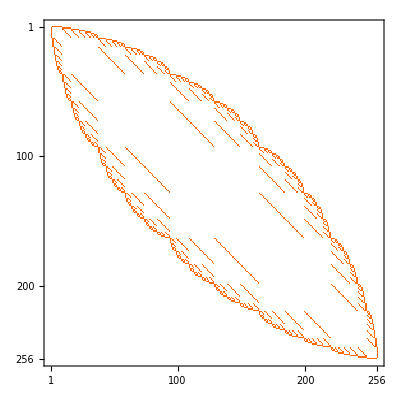

```mathematica
n=8;
Δ=Table[ConstantArray[0,{Binomial[n,i],Binomial[n,i]}],{i,0,n}];
(*Table[Δ[[i+1]]//MatrixForm,{i,0,n}]*)
f[n_Integer,l__]:=Module[
{},
ReplacePart[ConstantArray[0,n],Table[#[[i]]->1,{i,Length@#}]]&/@l
]
f[n,#]&/@Table[Subsets[Range[n],{i}],{i,0,n}];
couple[n_,np_]:=Module[
{states,couplings},
states=f[n,#]&/@Table[Subsets[Range[n],{i}],{i,np-1,np}];
couplings=Table[If[
Total[If[#[[1]]==#[[2]],0,1]&/@Transpose@{states[[1,i]],states[[2,j]]}]==1,
1,0],{i,Length@states[[1]]},{j,Length@states[[2]]}];
Return[couplings];
]
as=Table[couple[n,i],{i,n}]/2;
Table[as[[i]]//MatrixForm,{i,n}];
H=ArrayFlatten@Table[
Table[If[j==i-1,Transpose[as[[j]]],0]+If[j==i,Δ[[i]],0]+If[j==i+1,as[[i]],0],{j,Length@Δ}],
{i,Length@Δ}
];
MatrixPlot@H
```

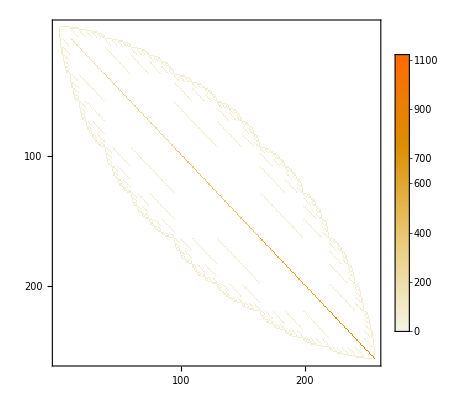

```mathematica
Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}];
Hb=ArrayFlatten@Table[
Table[If[j==i-1,Transpose[as[[j]]],0]+If[j==i,Δb[[i]],0]+If[j==i+1,as[[i]],0],{j,Length@Δb}],
{i,Length@Δb}
];
MatrixPlot@Hb
```

```mathematica
U[t_,H__]:=MatrixExp[-ⅈ 2π H t]
```

```mathematica
$PlotTheme="Detailed"
```

Detailed

```mathematica
ts=Range[0,1.5,0.001];
tsb=Range[0,1.5,0.001];
psis=U[#,H].UnitVector[Length@H,1]&/@ts;
psisb=U[#,Hb].UnitVector[Length@Hb,1]&/@tsb;
homos={};
blockaded={};
start=0;
stop=0;
For[i=0,i≤n,i+=1,
start=stop+1;
stop=start+Binomial[n,i]-1;
AppendTo[homos,Transpose@{ts,Total[Abs[#[[start;;stop]]]^2]&/@psis}];
AppendTo[blockaded,Transpose@{tsb,Total[Abs[#[[start;;stop]]]^2]&/@psisb}];
]
```

```mathematica
ll=LineLegend[97,{"|0ψ(t)|^2","|1ψ(t)|^2","|2ψ(t)|^2","|3ψ(t)|^2","|4ψ(t)|^2","|5ψ(t)|^2","|6ψ(t)|^2","|7ψ(t)|^2","|8ψ(t)|^2"}]
```

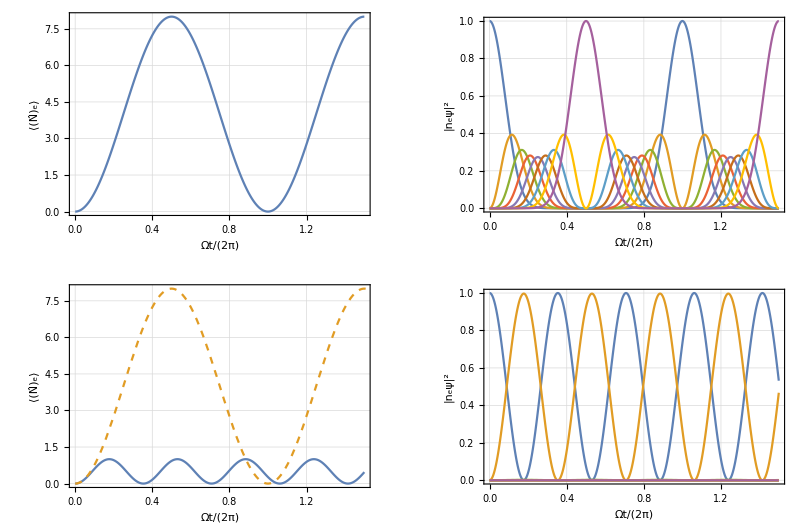

unblockaded_RFE_n=8.pdf

```mathematica
p=GraphicsGrid[{{
Show[
ListLinePlot[
{Transpose@{ts,Sum[(i-1)*homos[[i,All,2]],{i,2,n+1}]}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
]
],
ListLinePlot[homos,FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium],PlotRange->All
],
ll
},
{
Show[
ListLinePlot[
{Transpose@{tsb,Sum[(i-1)*blockaded[[i,All,2]],{i,2,n+1}]}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
],
Plot[{,n Sin[π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
ListLinePlot[blockaded,FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium],PlotRange->All
],
ll
}},ImageSize->800]
SetDirectory[NotebookDirectory[]];
Export["unblockaded_RFE_n="<>ToString[n]<>".pdf",p]
```

```mathematica
ClearAll[blockaded,homos]
```

```mathematica
nstop=4;
start=Sum[Binomial[n,i],{i,0,nstop-2}]+1;
stop=Sum[Binomial[n,i],{i,0,nstop}];
(*H[[start;;stop,start;;stop]]//MatrixForm*)
Binomial[n,nstop-1]
Binomial[n,nstop]
Binomial[n,nstop]/Binomial[n,nstop-1]
{e,v}=Eigensystem@H[[start;;stop,start;;stop]];
v=#/Norm[#]&/@v;

v[[1;;2]]//TableForm
e[[1;;2]]
√((n-ne+1)ne)/2/.{ne->nstop}
```

56

70

5/4

$Aborted

$Aborted[]

{-3/(√2),3/(√2)}

√5

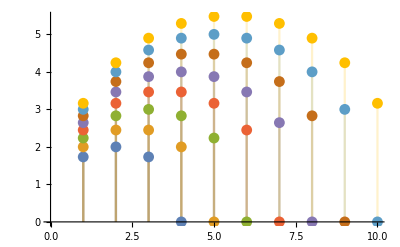

```mathematica
DiscretePlot[Evaluate[√((nn-ne+1)ne)/.nn->Range[3,10]],{ne,1,10},PlotRange->{0,All}]
```

```mathematica
Range[5]-5/2
```

{-3/2,-1/2,1/2,3/2,5/2}

```mathematica
√((5/2-m+1)(m+5/2))/.m->(Range[5]-5/2)
```

{√5,2 √2,3,2 √2,√5}

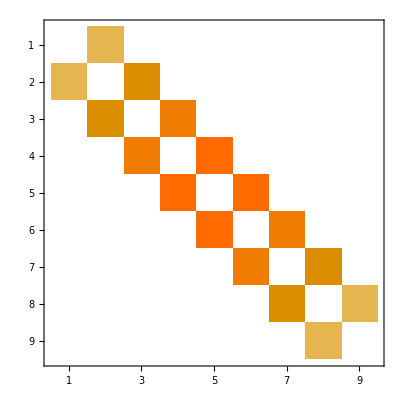

(0 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√2 | 0 | √(7/2) | 0 | 0 | 0 | 0 | 0 | 0
0 | √(7/2) | 0 | 3/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 3/(√2) | 0 | √5 | 0 | 0 | 0 | 0
0 | 0 | 0 | √5 | 0 | √5 | 0 | 0 | 0
0 | 0 | 0 | 0 | √5 | 0 | 3/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 3/(√2) | 0 | √(7/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | √(7/2) | 0 | √2
0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 | 0)

```mathematica
HJM=ArrayFlatten@Table[
Table[If[j==i-1,√((n-i+1)i)/2,0]+If[j==i+1,√((n-j+1)j)/2,0],{j,0,n}],
{i,0,n}
];
MatrixPlot@HJM
HJM//MatrixForm
tsJM=Range[0,1.5,0.001];
psisJM=U[#,HJM].UnitVector[Length@HJM,1]&/@tsJM;
JMs={};
For[i=1,i≤Length[HJM],i+=1,
AppendTo[JMs,Transpose@{tsJM,Abs[UnitVector[Length@HJM,i].#]^2&/@psisJM}];
]
```

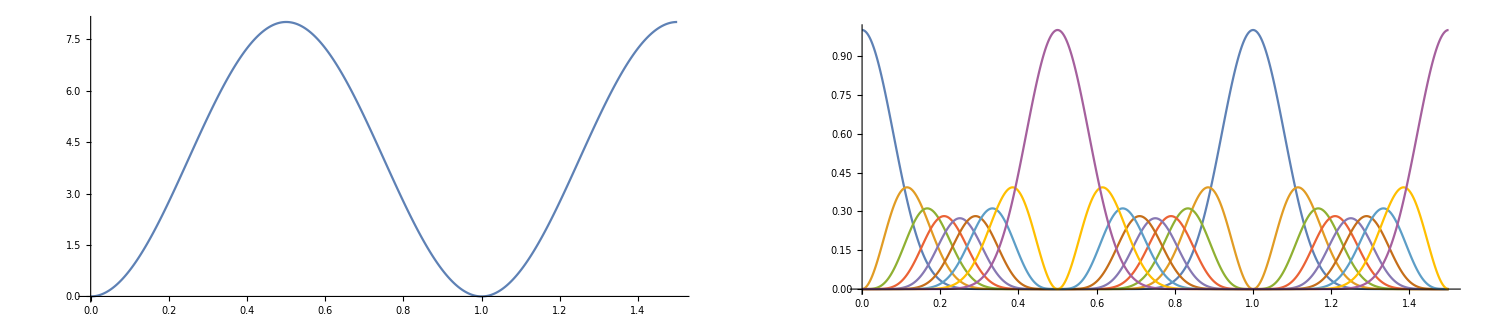

```mathematica
GraphicsRow[{
Show[
ListLinePlot[
{Transpose@{tsJM,Total@(Range[0,Length[JMs]-1]*JMs[[All,All,2]])}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
]
],
ListLinePlot[JMs,FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium],PlotRange->All
],
ll
}]
```

```mathematica
Hbperf=ArrayFlatten@{
{Δb[[1]],a as[[1]]},
{a Transpose[as[[1]]],Δb[[2]]}
}+DiagonalMatrix[{0,1,1,1}]d;
MatrixForm@Hbperf
{e,v}=Eigensystem@Hbperf;
v=v/Norm/@v;
e
v//Chop//MatrixForm
```

(0 | a/2 | a/2 | a/2
a/2 | d | 0 | 0
a/2 | 0 | d | 0
a/2 | 0 | 0 | d)

{d,d,1/2 (d-√(3 a^2+d^2)),1/2 (d+√(3 a^2+d^2))}

(0 | -1/(√2) | 0 | 1/(√2)
0 | -1/(√2) | 1/(√2) | 0
-(d+√(3 a^2+d^2))/(a √(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d+√(3 a^2+d^2))/a]^2))
-(d-√(3 a^2+d^2))/(a √(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)) | 1/(√(3+Abs[(d-√(3 a^2+d^2))/a]^2)))

```mathematica
n=5;
Hbperf=ArrayFlatten@{
{0,{Table[a[m],{m,n}]}},
{Transpose[{Table[a[m],{m,n}]}],DiagonalMatrix[ConstantArray[0,n]]}
};
MatrixForm@Hbperf
{e,v}=Eigensystem@Hbperf;
v=v/Norm/@v;
e
v//Chop//MatrixForm
```

(0 | a[1] | a[2] | a[3] | a[4] | a[5]
a[1] | 0 | 0 | 0 | 0 | 0
a[2] | 0 | 0 | 0 | 0 | 0
a[3] | 0 | 0 | 0 | 0 | 0
a[4] | 0 | 0 | 0 | 0 | 0
a[5] | 0 | 0 | 0 | 0 | 0)

{0,0,0,0,-√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2),√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2)}

(0 | -a[5]/(a[1] √(1+Abs[a[5]/a[1]]^2)) | 0 | 0 | 0 | 1/(√(1+Abs[a[5]/a[1]]^2))
0 | -a[4]/(a[1] √(1+Abs[a[4]/a[1]]^2)) | 0 | 0 | 1/(√(1+Abs[a[4]/a[1]]^2)) | 0
0 | -a[3]/(a[1] √(1+Abs[a[3]/a[1]]^2)) | 0 | 1/(√(1+Abs[a[3]/a[1]]^2)) | 0 | 0
0 | -a[2]/(a[1] √(1+Abs[a[2]/a[1]]^2)) | 1/(√(1+Abs[a[2]/a[1]]^2)) | 0 | 0 | 0
-(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[1]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[2]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[3]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[4]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | 1/(√(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2))
(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[1]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[2]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[3]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | a[4]/(a[5] √(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)) | 1/(√(1+Abs[a[1]/a[5]]^2+Abs[a[2]/a[5]]^2+Abs[a[3]/a[5]]^2+Abs[a[4]/a[5]]^2+Abs[(√(a[1]^2+a[2]^2+a[3]^2+a[4]^2+a[5]^2))/a[5]]^2)))

```mathematica
vnew=Orthogonalize[v[[3;;-1]]];
```

```mathematica
Simplify[vnew[[1]],Assumptions->a[1]>0&&a[5]>0]
Simplify[vnew[[2]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
Simplify[vnew[[3]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
Simplify[vnew[[4]],Assumptions->a[1]>0&&a[5]>0&&a[2]>0&&a[3]>0&&a[4]>0]
```

{0,-a[3]/(√(a[1]^2+Abs[a[3]]^2)),0,a[1]/(√(a[1]^2+Abs[a[3]]^2)),0,0}

{0,-(a[1] a[2])/(√((a[1]^2+a[3]^2) (a[1]^2+a[2]^2+a[3]^2))),√((a[1]^2+a[3]^2)/(a[1]^2+a[2]^2+a[3]^2)),-(a[2] a[3])/(√((a[1]^2+a[3]^2) (a[1]^2+a[2]^2+a[3]^2))),0,0}

$Aborted

$Aborted

```mathematica
Hbperf.DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}]-DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}].Hbperf//MatrixForm
```

(0 | a[1] d[1] | a[2] d[2] | a[3] d[3] | a[4] d[4] | a[5] d[5]
-a[1] d[1] | 0 | 0 | 0 | 0 | 0
-a[2] d[2] | 0 | 0 | 0 | 0 | 0
-a[3] d[3] | 0 | 0 | 0 | 0 | 0
-a[4] d[4] | 0 | 0 | 0 | 0 | 0
-a[5] d[5] | 0 | 0 | 0 | 0 | 0)

```mathematica
Hbperf.DiagonalMatrix[{0,d[1],d[2],d[3],d[4],d[5]}]//MatrixForm
```

(0 | a[1] d[1] | a[2] d[2] | a[3] d[3] | a[4] d[4] | a[5] d[5]
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

#### What is the correction to the wavefunction for expected numbers

```mathematica
n=5;

beam[p3_,Ω_,w0_,λ_]:=Module[
{w,zR,Rabi},
zR=π w0^2/λ;
w[z_]:=w0 Sqrt[1+(z/zR)^2];
Return[Ω(w0/w[x3[3]-p3[[3]]])Exp[-(((x3[1]-p3[[1]])^2+(x3[2]-p3[[2]])^2)/w[x3[3]-p3[[3]]]^2)]];
];

m=87*1.67*10^-27;
k=1.38*10^-23;

atoms[T_,ω3__]:=Module[{σx3,σv},
σx3=Sqrt[(k T)/(m #^2)]&/@ω3;
σv=Sqrt[(k T)/m];
Return[{σx3,σv}];
];

a=191Sqrt[0.75]; (* 780 Rabi Frequency (both A&B) Scaled with 480 to mimick observed rabi frequency*)
b=19.6Sqrt[0.75]; (* 480 Rabi Frequency Scaled with 480 to mimick observed rabi frequency *)
ΔP=1800; (* Intermediate State Detuning *)
δ=((b^2-a^2)/(4ΔP)); (* Real part of AC Stark Shift that can be accounted for *)
Γ=6; (* Intermediate State Linewidth *)
Ω1=(a b)/(2 ΔP); (* nominal rabi frequency *)
Print["Ω_(2  γ): ",Ω1];
nb=6; (* atom number *)
Δk=(1/.480-1/.780); (* Doppler shift from counter propagating lasers *)

atom=atoms[150*10^-6,{π 0.0829,π 0.0829,2π 0.003185}]; (* atom parameters *)
beam1=beam[{0,0,0},a,8,.780]; (* 780 Beam parameters *)
beam2=beam[{0,0,0},b,4.5,.480]; (* 480 Beam parameters *)

{σx3d,σv}=atom;

trials=10000;
v1fid={};
v2fid={};
v1ortho={};
v2ortho={};
v1v2={};

For[i=1,i≤trials,i+=1,

x3d=RandomVariate[NormalDistribution[0,#],n]&/@σx3d;
vz=RandomVariate[NormalDistribution[0,σv],n]; (* doppler only *)
δdopp=Δk*vz; (* only z contributes to doppler shift *)

(*Print["Doppler: ",δdopp];*)

posSubs=(Table[x3[i]->x3d[[i]],{i,3}]);
α=(beam1/.posSubs);
β=(beam2/.posSubs);

(* calculate the couplings between ground and ryd atoms *)
aas=(α β)/(4(ΔP+I Γ/2));
(*Print["αs: ",aas];*)
GR1={aas};

(* detunings due to inhomogeneous braodening go here *)
Δ1s=(β^2-α^2)/(4(ΔP+I Γ/2))-δdopp-δ;
R1R1=DiagonalMatrix[Δ1s];
(*Print["R1R1: ",MatrixForm[R1R1]];*)

Hbperf=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],R1R1}
};
(*Print["Hb perf: ",MatrixForm[Hbperf]];*)

A=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],DiagonalMatrix[ConstantArray[0,n]]}
};
(*Print["A: ",MatrixForm@A];*)

ΔΔ=ArrayFlatten@{
{0,{ConstantArray[0,n]}},
{Transpose@{ConstantArray[0,n]},R1R1}
};
(*Print["Δ1s: ",MatrixForm@ΔΔ];*)

(*MatrixForm@A*)
{e,v}=Eigensystem@A;
v=Orthogonalize@v;
v=v/Norm/@v;
(*e
v//Chop//MatrixForm*)
{ef,vf}=Eigensystem@Hbperf;
vf=Orthogonalize@vf;
vf=vf/Norm/@vf;
(*ef
vf//Chop//MatrixForm*)

(*Print["v1"];*)
crossovers=Table[Abs[v[[1]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v1fid,Max[crossovers]];
posv1=Ordering[crossovers,-1];

(*Print["v2"];*)
crossovers=Table[Abs[v[[2]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v2fid,Max[crossovers]];
posv2=Ordering[crossovers,-1];

AppendTo[v2ortho,Total[Delete[crossovers,{posv1,posv2}]]];

crossovers=Table[Abs[v[[1]].vf[[i]]]^2,{i,Length@v}];
AppendTo[v1ortho,Total[Delete[crossovers,{posv1,posv2}]]];

AppendTo[v1v2,Abs[v[[posv2[[1]]]].vf[[posv1[[1]]]]]^2];
]
```

Ω_(2  γ): 0.779917

```mathematica
MatrixForm@v//Chop
```

(0.707107 | -0.324438 | -0.312653 | -0.296901 | -0.322754 | -0.323524
0.707107 | 0.324438 | 0.312653 | 0.296901 | 0.322754 | 0.323524
0 | -0.442158-0.000237508 ⅈ | 0.865985 | -0.127263+0.0000770341 ⅈ | -0.138344+0.0000837419 ⅈ | -0.138674+0.0000839417 ⅈ
0 | -0.419881-0.000229347 ⅈ | -0.127263+0.0000758806 ⅈ | 0.879149 | -0.131374+0.000078332 ⅈ | -0.131687+0.0000785189 ⅈ
0 | -0.456443-0.000242344 ⅈ | -0.138344+0.0000846014 ⅈ | -0.131374+0.000080339 ⅈ | 0.857187 | -0.143154+0.000087543 ⅈ
0 | -0.457532-0.0002427 ⅈ | -0.138674+0.0000848709 ⅈ | -0.131687+0.0000805949 ⅈ | -0.143154+0.0000876127 ⅈ | 0.856504)

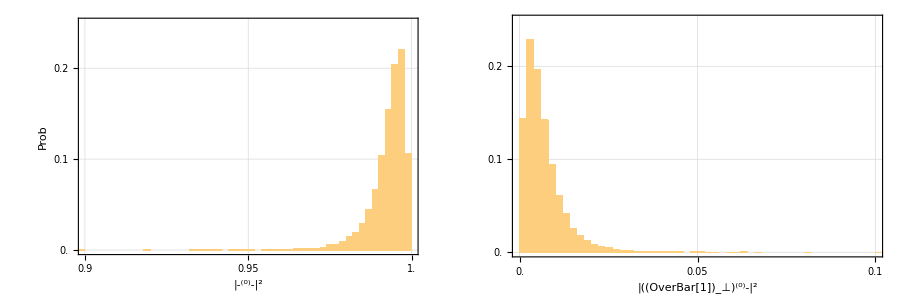

```mathematica
fs=24;
eigenproj=GraphicsRow[{
(Histogram[v2fid,Round@√trials,"Probability",FrameLabel->{"|-^(0)-|^2","Prob"
},ImageSize->Full,PlotRange->{{0.9,1},{0,0.25}},LabelStyle->Directive[Bold, FontSize->fs],FrameTicks->{Range[0.9,1,0.05],Range[0,0.3,0.1],None,None}]),
Histogram[v2ortho,Round@√trials,"Probability",FrameLabel->{"|((OverBar[1])_⊥)^(0)-|^2",""},ImageSize->Full,PlotRange->{{0,0.1},{0,0.25}},LabelStyle->Directive[Bold, FontSize->fs],FrameTicks->{Range[0,.1,0.05],Range[0,0.3,0.1],None,None}]
}
,ImageSize->900]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["eigenstateProj.pdf",eigenproj]
```

eigenstateProj.pdf

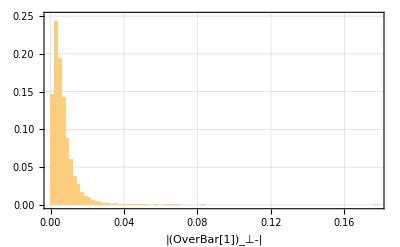

```mathematica
Histogram[v2ortho,Round@√trials,"Probability",FrameLabel->{"|(OverBar[1])_⊥-|",""},ImageSize->400,PlotRange->{0,0.25}]
```

```mathematica
v1v2
```

{0.000634927,0.000107273,0.00168484,0.984839,0.998709,0.995153,0.994303,0.979734,0.99716,0.99442,9980,0.993462,0.0000153194,0.000609609,0.00113965,0.997871,0.000103532,0.0000538167,0.000977754,0.00164463,0.994449}
 |  |  |  |

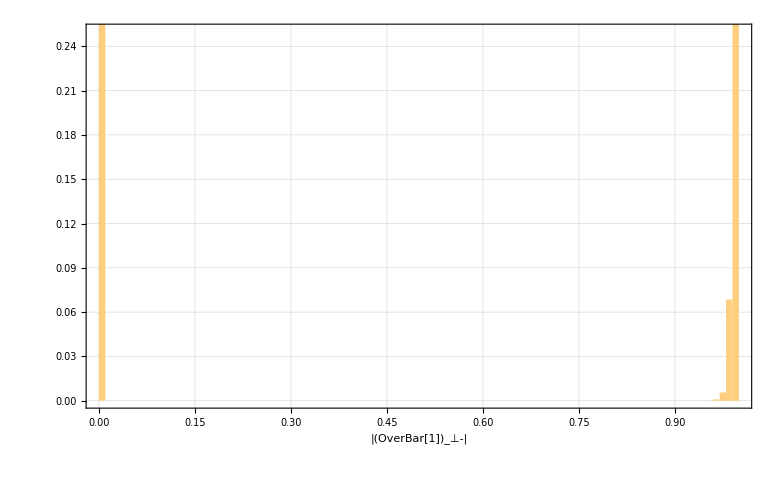

```mathematica
Histogram[v1v2,Round@√trials,"Probability",FrameLabel->{"|(OverBar[1])_⊥-|",""},ImageSize->400,PlotRange->{0,0.25}]
```

```mathematica
(√3)/(√2 √((√3)^2+0.1^2))
```

0.705931

#### expected speed up inhomogeneous broadening correction

```mathematica
n=5;

beam[p3_,Ω_,w0_,λ_]:=Module[
{w,zR,Rabi},
zR=π w0^2/λ;
w[z_]:=w0 Sqrt[1+(z/zR)^2];
Return[Ω(w0/w[x3[3]-p3[[3]]])Exp[-(((x3[1]-p3[[1]])^2+(x3[2]-p3[[2]])^2)/w[x3[3]-p3[[3]]]^2)]];
];

m=87*1.67*10^-27;
k=1.38*10^-23;

atoms[T_,ω3__]:=Module[{σx3,σv},
σx3=Sqrt[(k T)/(m #^2)]&/@ω3;
σv=Sqrt[(k T)/m];
Return[{σx3,σv}];
];

a=191Sqrt[0.75]; (* 780 Rabi Frequency (both A&B) Scaled with 480 to mimick observed rabi frequency*)
b=19.6Sqrt[0.75]; (* 480 Rabi Frequency Scaled with 480 to mimick observed rabi frequency *)
ΔP=1800; (* Intermediate State Detuning *)
δ=((b^2-a^2)/(4ΔP)); (* Real part of AC Stark Shift that can be accounted for *)
Γ=6; (* Intermediate State Linewidth *)
Ω1=(a b)/(2 ΔP); (* nominal rabi frequency *)
Print["Ω_(2  γ): ",Ω1];
nb=6; (* atom number *)
Δk=(1/.480-1/.780); (* Doppler shift from counter propagating lasers *)

atom=atoms[150*10^-6,{π 0.0829,π 0.0829,2π 0.003185}]; (* atom parameters *)
beam1=beam[{0,0,0},a,8,.780]; (* 780 Beam parameters *)
beam2=beam[{0,0,0},b,4.5,.480]; (* 480 Beam parameters *)

{σx3d,σv}=atom;

trials=10000;
es={};
efs={};

For[i=1,i≤trials,i+=1,

x3d=RandomVariate[NormalDistribution[0,#],n]&/@σx3d;
vz=RandomVariate[NormalDistribution[0,σv],n]; (* doppler only *)
δdopp=Δk*vz; (* only z contributes to doppler shift *)

(*Print["Doppler: ",δdopp];*)

posSubs=(Table[x3[i]->x3d[[i]],{i,3}]);
α=(beam1/.posSubs);
β=(beam2/.posSubs);

(* calculate the couplings between ground and ryd atoms *)
aas=(α β)/(4(ΔP+I Γ/2));
(*Print["αs: ",aas];*)
GR1={aas};

(* detunings due to inhomogeneous braodening go here *)
Δ1s=(β^2-α^2)/(4(ΔP+I Γ/2))-δdopp-δ;
R1R1=DiagonalMatrix[Δ1s];
(*Print["R1R1: ",MatrixForm[R1R1]];*)

Hbperf=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],R1R1}
};
(*Print["Hb perf: ",MatrixForm[Hbperf]];*)

A=ArrayFlatten@{
{0,{aas}},
{Transpose[{aas}],DiagonalMatrix[ConstantArray[0,n]]}
};
(*Print["A: ",MatrixForm@A];*)

ΔΔ=ArrayFlatten@{
{0,{ConstantArray[0,n]}},
{Transpose@{ConstantArray[0,n]},R1R1}
};
(*Print["Δ1s: ",MatrixForm@ΔΔ];*)

(*MatrixForm@A*)
{e,v}=Eigensystem@A;
v=Orthogonalize@v;
v=v/Norm/@v;
(*e
v//Chop//MatrixForm*)
{ef,vf}=Eigensystem@Hbperf;
vf=Orthogonalize@vf;
vf=vf/Norm/@vf;
(*ef
vf//Chop//MatrixForm*)

AppendTo[es,(2{Max[Re@e],Min[Re@e]}/Ω1)^2/n];
AppendTo[efs,(2{Max[Re@ef],Min[Re@ef]}/Ω1)^2/n];
]
```

Ω_(2  γ): 0.779917

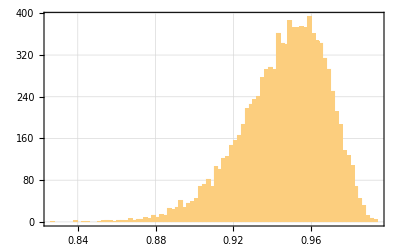

0.945784

0.972514

0.92

0.959166

0.0218473

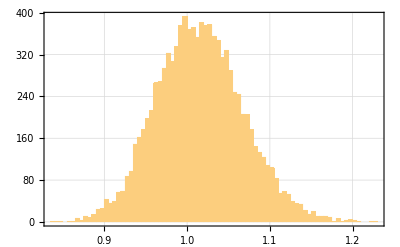

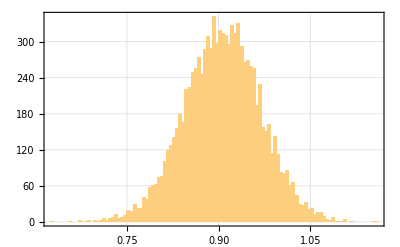

```mathematica
Histogram[es[[All,1]],Round@√trials]
Mean[es[[All,1]]]
Mean[es[[All,1]]]^(1/2)
0.92
0.92^(1/2)
StandardDeviation[es[[All,1]]]
Histogram[efs[[All,1]],Round@√trials]
Histogram[efs[[All,2]],Round@√trials]
```

```mathematica
Eigensystem@ArrayFlatten@{
{0,{ConstantArray[1/2,5]}},
{Transpose[{ConstantArray[1/2,5]}],0}
}
```

{{-(√5)/2,(√5)/2,0,0,0,0},{{-√5,1,1,1,1,1},{√5,1,1,1,1,1},{0,-1,0,0,0,1},{0,-1,0,0,1,0},{0,-1,0,1,0,0},{0,-1,1,0,0,0}}}

#### Time Series for non-symmetric singly excited state

Dot::dotsh: Tensors {0, 1, 1, 1, 0, 0, 0, 0} and {0.  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.57735  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ, 0.  + 0.\ ⅈ} have incompatible shapes.

Dot::dotsh: Tensors {0, 1, 1, 1, 0, 0, 0, 0} and {4.48957×10^-9 - 0.00544128\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, 0.577325  + 1.42756×10^-6\ ⅈ, -0.0000170495 + 7.13767×10^-7\ ⅈ, -0.0000170495 + 7.13767×10^-7\ ⅈ, -0.000453445 - 0.00358944\ ⅈ, « 18 », -5.31566×10^-6 + 1.84992×10^-6\ ⅈ, 3.04899×10^-8 + 4.20602×10^-8\ ⅈ, 3.04899×10^-8 + 4.20602×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 2.03265×10^-8 + 2.804×10^-8\ ⅈ, 8.47704×10^-11 - 1.32586×10^-10\ ⅈ} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

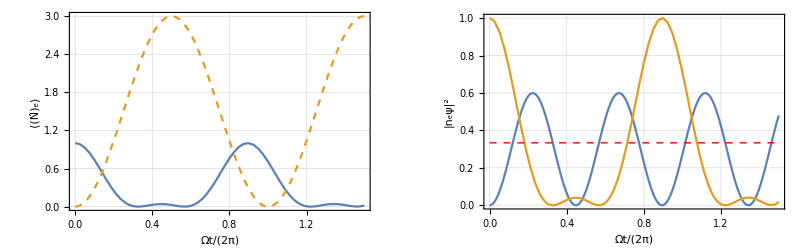

```mathematica
n=3;
k=3;
tsb=Range[0,1.5,0.001];
ψ0=Sum[UnitVector[Length@Hb,i+1]/√k,{i,k}];
onebars=Abs[(1/√3){0,1,1,1,0,0,0,0}.#]^2&/@psisb;
psisb=U[#,Hb].ψ0&/@tsb;
gsb=Transpose@{ts,Abs[UnitVector[Length@Hb,1].#]^2&/@psisb};
onesb=Transpose@{ts,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};
p2=GraphicsRow[
{
Show[
ListLinePlot[
{Transpose@{tsb,Total@{onesb[[All,2]]}}},
ImageSize->Full,FrameLabel->{"Ωt/(2π)","⟨(N̂)_e⟩"},PlotRange->{0,n},LabelStyle->Directive[Medium],ImagePadding->{{Automatic, 10}, {Automatic, 10}}
],
Plot[{,n Sin[π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
Show[
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
Graphics[{Red,Dashed,Thick,Line[{{0,1/n},{tsb[[-1]],1/n}}]}]
],
ll
},ImageSize->800]
(*Export["nonwstate_RFE.pdf",p2]*)
```

3/5

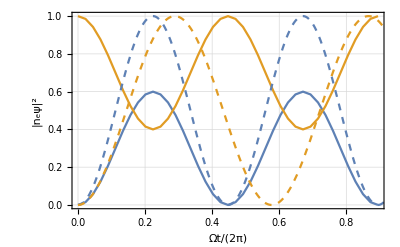

```mathematica
n=5;
k=3;
Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}];
as=Table[couple[n,i],{i,n}]/2;

Hbperf=ArrayFlatten@{
{Δb[[1]],as[[1]]},
{Transpose[as[[1]]],Δb[[2]]}
};
tb=1/√n;
tsb=Range[0,2tb,tb/20];

ψ0=Sum[UnitVector[Length@Hbperf,i+1]/√k,{i,k}];

overlap=Abs[((1/√n)Sum[UnitVector[Length@Hbperf,k+1],{k,n}]).ψ0]^2+Abs[ψ0[[1]]]^2

psisb=U[#,Hbperf].ψ0&/@tsb;
gsb=Transpose@{tsb,Abs[UnitVector[Length@Hbperf,1].#]^2&/@psisb};
onesb=Transpose@{tsb,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};

p2=GraphicsRow[{
Show[
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]],
Plot[{ Sin[√n π t]^2, Sin[√k π t]^2},{t,0,2},PlotStyle->Dashed,PlotLegends->None]
],
ll
},ImageSize->800]
```

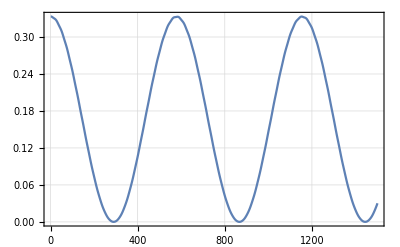

```mathematica
ListLinePlot@onebars
```

{0.380331+0. ⅈ,0.921005+0.084251 ⅈ,0.+0. ⅈ,0.+0. ⅈ}

0.429768

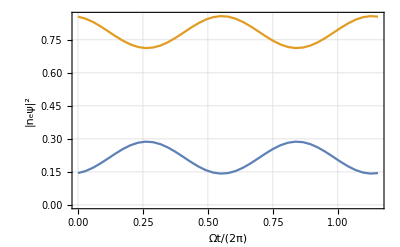

```mathematica
n=3;

Δb=Table[DiagonalMatrix[ConstantArray[i(i-1)*20,Binomial[n,i]]],{i,0,n}];
as=Table[couple[n,i],{i,n}]/2;

Hbperf=ArrayFlatten@{
{Δb[[1]],as[[1]]},
{Transpose[as[[1]]],Δb[[2]]}
};
tb=1/√n;
tsb=Range[0,2tb,tb/20];

ψ0gen[{θ_,ϕ_}]:=Sin[θ]UnitVector[Length@Hbperf,1]+Cos[θ]Exp[ⅈ ϕ]UnitVector[Length@Hbperf,2];
ψ0=ψ0gen[RandomReal[{0,2π},2]]

overlap=Abs[((1/√n)Sum[UnitVector[Length@Hbperf,k+1],{k,n}]).ψ0]^2+Abs[ψ0[[1]]]^2

psisb=U[#,Hbperf].ψ0&/@tsb;
gsb=Transpose@{tsb,Abs[UnitVector[Length@Hbperf,1].#]^2&/@psisb};
onesb=Transpose@{tsb,Total[Abs[#[[2;;n+1]]]^2]&/@psisb};

p2=GraphicsRow[{
ListLinePlot[{gsb,onesb},FrameLabel->{"Ωt/(2π)","|n_eψ|^2"},ImageSize->Full,LabelStyle->Directive[Medium]
],
ll
},ImageSize->800]
```

#### Full Seperable State limits

```mathematica
ndata={};
nlist={2,3,5,8,10};
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
data={};

For[l=1,l≤100000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{π 0.9,1.1π},{n,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
Print[n];
AppendTo[ndata,{n,data}];
]
```

2

3

5

8

10

```mathematica
ndataold=ndata;
```

```mathematica
GraphicsColumn[(ListPlot[#[[All,2]],PlotRange->{{0,1},{0,1}},PlotLabel->"n="<>ToString[#[[1,1]]],ImageSize->Full]&/@Transpose@{ndataold,ndata}),ImageSize->400]
```

-Graphics-

#### Partially separable state limits

```mathematica
ndata={};
nlist=Range[4,8];
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
kdata={};
For[kk=3,kk≤3,kk+=1,
data={};
(*number separable subspaces*)
subspaces=Ceiling[n/kk];
ks=ConstantArray[kk,subspaces];
(*make sure sum of ks equals n*)
ks[[-1]]=n-(subspaces-1)*kk;

For[l=1,l≤50000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{0,2π},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
√ks[[j]] spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
For[l=1,l≤50000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{3π/4,5π/4},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(1/n)Abs[
Sum[
√ks[[j]] spinStates[[j,2]]*
Product[spinStates[[k,1]],{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
]
]^2;
AppendTo[data,{p0,p1}];
]
(*Print["k: ",kk];*)
AppendTo[kdata,{kk,data}];
]
Print[n];
AppendTo[ndata,{n,kdata}];
]
```

4

5

6

7

8

```mathematica
$PlotTheme="Detailed";
```

```mathematica
plot=GraphicsGrid@Table[(
Show[
ListPlot[ndata[[k,2,#,2]],ImageSize->250,PlotRange->{{0,1},{0,1}},FrameLabel->{"P0","P1"},PlotLabel->"n="<>ToString[ndata[[k,1]]]<>", k="<>ToString[ndata[[k,2,#,1]]]],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/ndata[[k,1]],{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]&/@Range[Length@ndata[[k,2]]]),
{k,Length@ndata}
];
```

```mathematica
Style[plot,Antialiasing->False]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Reichel_numerical_kpartite.png",plot]
```

Reichel_numerical_kpartite.png

```mathematica
ClearAll[lines];
```

```mathematica
binnum=200;
f[l__]:=Floor[l[[1]],1/binnum]
g[x__]:={N@Floor[x[[1,1]],1/binnum],Max[x[[All,2]]]}
For[m=1,m≤Length@ndata,m+=1,
nn=nlist[[m]];
For[k=3,k<4,k+=1,
(*Print[{nn,k}];*)
ll=GatherBy[ndata[[m,2,1,2]],f];
lines[nn][k]=Interpolation[Sort[g/@ll,#1[[1]]<#2[[1]]&]];
];
]
```

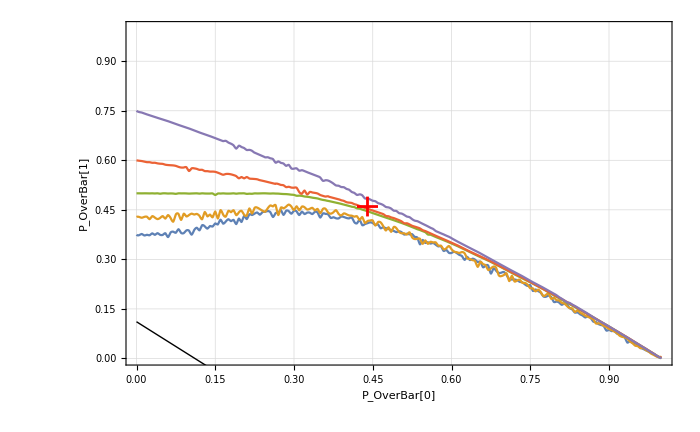

```mathematica
Show[
Plot[Evaluate@Table[lines[m][3][x],{m,8,4,-1}],{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P_OverBar[0]","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18]],
point,
Plot[-x+1/9,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
p=Show[-Graphics-,point2]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
Export["Reichel_k=3_thresholds_2015_06_04.pdf",p]
Export["Reichel_k=3_thresholds_2015_06_04.png",p]
```

Reichel_k=3_thresholds_2015_06_04.pdf

Reichel_k=3_thresholds_2015_06_04.png

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Reichel_k=3_thresholds.pdf",%%]
```

/home/ebert/Dropbox/thesis/introduction/figures

Reichel_k=3_thresholds.pdf

```mathematica
Show[
Plot[Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,3}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][3][x],{m,16,4,-1}],{x,0,1},PlotRange->{0,1}],
Plot[-x+1,{x,0,1},PlotStyle->{Gray,Dashed},PlotRange->{0,1}]
]
```

-Graphics-

```mathematica
Show[
Plot[Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,3}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][3][x],{m,16,4,-1}],{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P0","P1"},PlotLabel->"k=3,4"],
Plot[{,Sum[PDF[PoissonDistribution[7.6],m](1-x),{m,1,4}]+Sum[PDF[PoissonDistribution[7.6],m]lines[m][4][x],{m,16,5,-1}]},{x,0,1},PlotRange->{0,1},PlotLegends->None,ImageSize->700,FrameLabel->{"P0","P1"},PlotLabel->"k=4"],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/4,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

-Graphics-

```mathematica
$PlotTheme="Detailed";
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
0.44+/-0.2
0.46+/-0.3
```

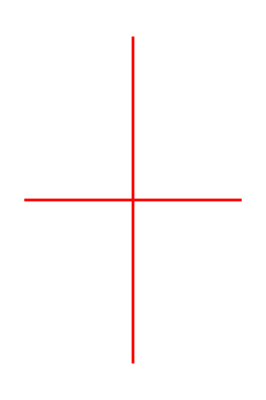

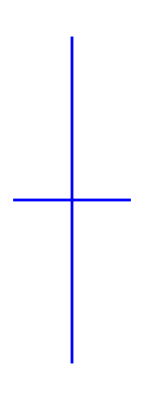

```mathematica
point=Graphics[{
Red,AbsoluteThickness[2],
Line[{{0.42,0.46},{0.46,0.46}}],
Line[{{0.44,0.43},{0.44,0.49}}]
}]
point2=Graphics[{
Blue,AbsoluteThickness[2],
Line[{{0.473-0.018,0.527},{0.473+0.018,0.527}}],
Line[{{0.473,0.527-0.0498},{0.473,0.527+0.0498}}]
}]
```

```mathematica
pnew=Show[
Plot[Evaluate@Table[k/9(1-p00),{k,6,9,1}],{p00,0,1},PlotRange->{0,1.05},PlotLegends->None(*{"k=2","k=4","k=6"}*),PlotStyle->AbsoluteThickness[1],FrameLabel->{"P_OverBar[0]","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18],ImageSize->500],
(*ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],*)
point,point2,
Plot[-x+1/9,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
Export["PerfectBlockadeThresholds_2015_06_04.pdf",pnew]
Export["PerfectBlockadeThresholds_2015_06_04.png",pnew]
```

PerfectBlockadeThresholds_2015_06_04.pdf

PerfectBlockadeThresholds_2015_06_04.png

```mathematica
0.48/0.58
```

0.827586

```mathematica
Show[
Plot[Evaluate@Table[k/7(1-p00),{k,3,7,2}],{p00,0,1},PlotRange->{0,1.1},PlotLegends->None(*{"k=2","k=4","k=6"}*),PlotStyle->Dashed,FrameLabel->{"P_0","P_OverBar[1]"},PlotLabel->"",LabelStyle->Directive[FontSize->18],ImageSize->500],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}],
Plot[-x+1/4,{x,0,1},PlotStyle->{Thick,Black},PlotLegends->None]
]
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["PerfectBlockadeThresholds.pdf",pnew]
```

/home/ebert/Dropbox/thesis/introduction/figures

PerfectBlockadeThresholds.pdf

```mathematica
DiscretePlot[PDF[PoissonDistribution[7.6],m],{m,0,20}]
```

-Graphics-

```mathematica
f/@{{0.1,1},{0.021,1},{0.001,2},{0.02,3}}
```

{1/10,1/50,0,1/50}

```mathematica
GatherBy[{{0.1,1},{0.021,1},{0.001,2},{0.02,3}},f]
```

{{{0.1,1}},{{0.021,1},{0.02,3}},{{0.001,2}}}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Reichel_numerical_kpartite_n=8_6_4_k=n-1.pdf",plot2]
```

Reichel_numerical_kpartite_n=8_6_4_k=n-1.pdf

#### partially separable states

```mathematica
ndata={};
nlist=Range[3,8];
For[k=1,k≤Length@nlist,k+=1,

n=nlist[[k]];
kdata={};
For[kk=2,kk<n,kk+=1,
data={};
(*number separable subspaces*)
subspaces=Ceiling[n/kk];
ks=ConstantArray[kk,subspaces];
(*make sure sum of ks equals n*)
ks[[-1]]=n-(subspaces-1)*kk;

For[l=1,l≤10000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{0,2π},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(*(1/n)*)
Sum[Abs[(*√ks[[j]]*)spinStates[[j,2]]]^2*
Product[Abs[spinStates[[k,1]]]^2,{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
];
AppendTo[data,{p0,p1}];
]
For[l=1,l≤10000,l+=1,

spinStates={Cos[#[[1]]],Sin[#[[1]]]Exp[ⅈ #[[2]]]}&/@RandomReal[{π/2,3π/2},{subspaces,2}];

p0=Product[spinStates[[k,1]]^2,{k,Length@spinStates}];
p1=(*(1/n)*)
Sum[Abs[(*√ks[[j]]*)spinStates[[j,2]]]^2*
Product[Abs[spinStates[[k,1]]]^2,{k,Delete[Range[Length@spinStates],j]}],
{j,Length@spinStates}
];
AppendTo[data,{p0,p1}];
]
(*Print["k: ",kk];*)
AppendTo[kdata,{kk,data}];
]
Print[n];
AppendTo[ndata,{n,kdata}];
]
```

3

4

5

6

7

8

```mathematica
plot=GraphicsGrid@Table[(
Show[
ListPlot[ndata[[k,2,#,2]],ImageSize->250,PlotRange->{{0,1},{0,1}},FrameLabel->{"P0","P1"},PlotLabel->"n="<>ToString[ndata[[k,1]]]<>", k="<>ToString[ndata[[k,2,#,1]]]],
ListLinePlot[Table[{1-0.48Sin[ϕ/2]^2-0.1,0.48Sin[ϕ/2]^2+0.1},{ϕ,0,2π,0.01}],PlotStyle->{Thick,Red}]
]&/@Range[Length@ndata[[k,2]]]),
{k,Length@ndata}
];
```

```mathematica
Style[plot,Antialiasing->False]
```

-Graphics-

#### Square Root Speed up

```mathematica
f[n_,kbar_,t_]:=Sum[PDF[PoissonDistribution[n],j] Sin[√(j-kbar)π t]^2,{j,kbar,30}]+Sum[PDF[PoissonDistribution[n],j] Sin[π t]^2,{j,kbar}]
```

```mathematica
normal[t_]:=f[7.6,0,t]
singleatom[t_]:=f[7.6,30,t]
kbar1[t_]:=f[7.6,1,t]
Plot[{normal[t],kbar1[t],singleatom[t]},{t,0,0.5},PlotRange->{0,1.05}]
```

-Graphics-

Lets do the fits we would expect

```mathematica
kbar1fit={#,NonlinearModelFit[Table[{t,f[#,1,t]},{t,0,0.5,0.04}],a f[nb,0,t],{{a,1},{nb,#}},t]}&/@Range[3,16];
kbar2fit={#,NonlinearModelFit[Table[{t,f[#,2,t]},{t,0,0.5,0.04}],a f[nb,0,t],{{a,1},{nb,#}},t]}&/@Range[3,16];
```

```mathematica
Plot[Evaluate@(#[[2]][t]&/@kbar1fit),{t,0,0.5},PlotLegends->None]
```

-Graphics-

```mathematica
kbar1data={#[[1]],nb/.#[[2]]["BestFitParameters"]}&/@kbar1fit;
Fit[kbar1data,{1,x},x]
kbar2data={#[[1]],nb/.#[[2]]["BestFitParameters"]}&/@kbar2fit;
Fit[kbar2data,{1,x},x]
Show[
Plot[{x,0.92x},{x,0,20},PlotStyle->{Directive[Thick,Black],Directive[Thick,Red,Dashed]}],
ListPlot[{kbar1data,kbar2data},PlotRange->{{0,20},{0,20}}]
]
```

-1.07665+1.00733 x

-2.06741+1.00783 x

-Graphics-

#### maths

```mathematica
state=Flatten@TensorProduct[Delete[Table[{a[i],b[i]},{i,3}],0]];

stateW=Sum[state/.Flatten@Table[If[j==i,{a[i]->0,b[i]->1},{a[i]->1,b[i]->0}],{i,3}],
{j,3}]

P0=TensorProduct[Transpose[{state}],{state}]/.Flatten@Table[{a[i]->1,b[i]->0},{i,3}]//ArrayFlatten;
P1=Sum[
TensorProduct[Transpose[{state}],{state}]/.Flatten@Table[If[j==i,{a[i]->0,b[i]->1},{a[i]->1,b[i]->0}],{i,3}],
{j,3}]//ArrayFlatten;
MatrixForm@P0
Conjugate[state].P0.state

MatrixForm@P1
Conjugate[state].P1.state

stateW.state
```

{0,1,1,0,1,0,0,0}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

a[1] a[2] a[3] Conjugate[a[1] a[2] a[3]]

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

a[2] a[3] b[1] Conjugate[a[2] a[3] b[1]]+a[1] a[3] b[2] Conjugate[a[1] a[3] b[2]]+a[1] a[2] b[3] Conjugate[a[1] a[2] b[3]]

a[2] a[3] b[1]+a[1] a[3] b[2]+a[1] a[2] b[3]

```mathematica
√0.96
```

0.979796

```mathematica
TensorProduct[IdentityMatrix[2],{{0,1},{1,0}}]//MatrixForm
TensorProduct[{{0,1},{1,0}},IdentityMatrix[2]]//MatrixForm
```

((0 | 1
1 | 0) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (0 | 1
1 | 0))

((0 | 0
0 | 0) | (1 | 0
0 | 1)
(1 | 0
0 | 1) | (0 | 0
0 | 0))

```mathematica
TensorProduct[{{1,0},{0,-1}},IdentityMatrix[2]]//MatrixForm
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (-1 | 0
0 | -1))

```mathematica
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
```

```mathematica
sx4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σx],If[i≠2,IdentityMatrix[2],σx],If[i≠3,IdentityMatrix[2],σx],If[i≠4,IdentityMatrix[2],σx]],
{i,4}
],4]];
sy4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σy],If[i≠2,IdentityMatrix[2],σy],If[i≠3,IdentityMatrix[2],σy],If[i≠4,IdentityMatrix[2],σy]],
{i,4}
],4]];
sz4=ArrayFlatten[ArrayFlatten[Sum[
TensorProduct[If[i≠1,IdentityMatrix[2],σz],If[i≠2,IdentityMatrix[2],σz],If[i≠3,IdentityMatrix[2],σz],If[i≠4,IdentityMatrix[2],σz]],
{i,4}
],4]];
MatrixForm/@{sx4,sy4,sz4}

state1=Flatten@(TensorProduct[{1,0},{0,1},{0,1},{0,1}]+TensorProduct[{0,1},{1,0},{0,1},{0,1}]+TensorProduct[{0,1},{0,1},{1,0},{0,1}]+TensorProduct[{0,1},{0,1},{0,1},{1,0}]);
state2=Flatten@(TensorProduct[{1,0},{0,1},{0,1},{0,1}]+TensorProduct[{0,1},{1,0},{0,1},{0,1}]-TensorProduct[{0,1},{0,1},{1,0},{0,1}]-TensorProduct[{0,1},{0,1},{0,1},{1,0}]);

jsq4=(sx4.sx4+sy4.sy4+sz4.sz4)/4;
MatrixForm@jsq4

(jsq4.state1)
state1

(jsq4.state2)
state2
```

{(0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0),(0 | -ⅈ | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0 | -ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | -ⅈ | -ⅈ | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | ⅈ | 0 | ⅈ | ⅈ | 0),(4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4)}

(6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 3 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6)

{0,0,0,0,0,0,0,6,0,0,0,6,0,6,6,0}

{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}

{0,0,0,0,0,0,0,2,0,0,0,2,0,-2,-2,0}

{0,0,0,0,0,0,0,1,0,0,0,1,0,-1,-1,0}

```mathematica
{e,v}=Eigensystem[jsq4];
e
v//MatrixForm
```

{6,6,6,6,6,2,2,2,2,2,2,2,2,2,0,0}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayFlatten@TensorProduct[Transpose[{state1}],{state1}]//MatrixForm
sx4;
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ArrayFlatten@TensorProduct[Transpose[{state2}],{state2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)